# ЛР5 (Бусько Егор, 3 вариант)

```mathematica
a=9;
f[x_,t_]:=E^(x*t);
u[0,t_]:=t^2;
u[2,t_]:=1;
u[x_,0]:=Cos[x];
h=0.05;
n=2/h;
m=3/h;
Table[x[i]=i*h,{i,0,n}];
Table[t[i]= i*h,{i,0,m}];
Table[Subscript[y, i,0]=u[x[i],0],{i,0,n}];
Table[Subscript[y, 0,i]=u[0,t[i]],{i,0,m}];
Table[Subscript[y, n,i]=u[2,t[i]],{i,0,m}];
Do[
Subscript[y, i,k+1]=Subscript[y, i,k]+a^2(Subscript[y, i-1,k]+Subscript[y, i+1,k]-2 Subscript[y, i,k])+ h f[x[i],t[k]],{k,0,m-1},{i,1,n-1}
]
```

```mathematica
res=Table[{x[i],t[k],Subscript[y, i,k]},{i,0,n/5},{k,0,m/5}];
```

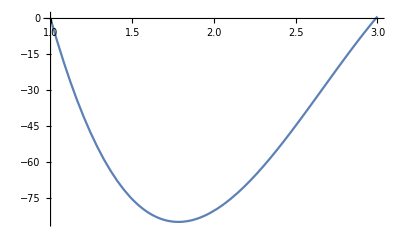

```mathematica
g[k_]:=Table[Subscript[y, i,k],{i,0,n}];
Interpolation[g[1]];
Plot[Interpolation[g[1]][x],{x,1,3}]
```